```mathematica
μPP[n_, c_, Γ_, K_]:=c+Γ*K*n^(Γ-1)/(Γ-1)
PPP[n_, Γ_, K_]:=K*n^Γ
epsPP[n_,c_,Γ_,K_]:=c*n+K*n^Γ/(Γ-1)
csPP[n_,c_,Γ_,K_]:=(Γ*PPP[n, Γ, K])/(PPP[n, Γ, K]+epsPP[n,c, Γ, K])
```

```mathematica
nextΓ[μ0_,μ1_,K0_,n0_,n1_,Γ0_]:=Γ/.FindRoot[(Γ K0 n0^(-Γ+Γ0) (-n0^(-1+Γ)+n1^(-1+Γ)))/(1-Γ)-μ0+μ1,{Γ,1.5},PrecisionGoal->6]
nextK[n0_,Γ1_,P0_]:=n0^-Γ1 P0
nextc[μ1_,n1_,K1_,Γ1_]:=μ1-(K1 n1^(-1+Γ1) Γ1)/(Γ1-1)
nextP[n1_,Γ1_,K1_]:=K1 n1^Γ1
```

#### Polytropic interpolation for Hebeler stiff plus 3

```mathematica
n0=0.16;(**fm^-3**)
neutronmass=939.5654205;(**MeV**)
hbarc=197.32698;(**MeV fm**)
```

```mathematica
Nucldat=Transpose[Import[NotebookDirectory[]<>"input/EoS_Hebeler.csv","CSV"]];
Length[Nucldat];
EoSIII=Transpose[Import[NotebookDirectory[]<>"input/EoS_III.csv","CSV"]];
nEoSIII=EoSIII[[1]]*n0/(neutronmass/hbarc)^3;
PEoSIII=EoSIII[[2]]*hbarc^3/neutronmass^4;
ϵEoSIII=EoSIII[[3]]*hbarc^3/neutronmass^4;
μEoSIII=EoSIII[[4]]/(neutronmass/1000);
```

```mathematica
Clear[Γarr,carr,Karr,Parr,narr,μarr]
novern0=Nucldat[[1]][[;;6]];
narr=novern0*n0/(neutronmass/hbarc)^3;
PNucl=Nucldat[[13]][[;;6]]*hbarc^3/neutronmass^4;
ϵNucl=Nucldat[[14]][[;;6]]*hbarc^3/neutronmass^4;
μarr=Table[(ϵNucl[[i]]+PNucl[[i]])/narr[[i]],{i,Length[narr]}];
(** EoS III **)
AppendTo[narr,1.1*n0/(neutronmass/hbarc)^3];
AppendTo[narr,1.5*n0/(neutronmass/hbarc)^3];
AppendTo[narr,3.9*n0/(neutronmass/hbarc)^3];
AppendTo[μarr,0.9775/(neutronmass/1000)];
AppendTo[μarr,1.122/(neutronmass/1000)];
AppendTo[μarr,1.369/(neutronmass/1000)];
Γ00=5/3//N;
c00=1;
Γarr = Table[0,{i,Length[narr]+1}];
carr = Table[0,{i,Length[narr]+1}];
Karr = Table[0,{i,Length[narr]+1}];
Parr = Table[0,{i,Length[narr]+1}];
epsarr = Table[0,{i,Length[narr]+1}];
Γarr[[1]]=Γ00;
carr[[1]]=c00;
Karr[[1]]=(μarr[[1]]-carr[[1]])*(Γarr[[1]]-1)*narr[[1]]^(1-Γarr[[1]])/Γarr[[1]];
Parr[[1]]=Karr[[1]]*narr[[1]]^Γarr[[1]];
epsarr[[1]]=epsPP[narr[[1]],carr[[1]],Γarr[[1]],Karr[[1]]];
For[i=2,i<=Length[narr],i++,
Γarr[[i]]=nextΓ[μarr[[i-1]],μarr[[i]],Karr[[i-1]],narr[[i-1]],narr[[i]],Γarr[[i-1]]];
Karr[[i]]=nextK[narr[[i-1]],Γarr[[i]],Parr[[i-1]]];
carr[[i]]=nextc[μarr[[i]],narr[[i]],Karr[[i]],Γarr[[i]]];
Parr[[i]]=nextP[narr[[i]],Γarr[[i]],Karr[[i]]];
epsarr[[i]]=epsPP[narr[[i]],carr[[i]],Γarr[[i]],Karr[[i]]];
Print[Γarr[[i]], " ",Karr[[i]], " ",carr[[i]], " ",Parr[[i]]]
]
nadd =0.04;
Γarr[[Length[Γarr]]]=Γarr[[Length[Γarr]-1]];
Karr[[Length[Karr]]]=Karr[[Length[Karr]-1]];
carr[[Length[carr]]]=carr[[Length[carr]-1]];
Parr[[Length[Parr]]]=PPP[nadd, Γarr[[Length[Γarr]]], Karr[[Length[Karr]]]];
AppendTo[narr,nadd]
AppendTo[μarr,μPP[nadd, carr[[Length[carr]]], Γarr[[Length[carr]]], Karr[[Length[carr]]]]]
Print[Γarr[[Length[Γarr]]], " ",Karr[[Length[Karr]]], " ",carr[[Length[carr]]], " ",Parr[[Length[Parr]]]];
```

2.44522 200.304 1.00599 0.000010563

2.32993 90.8951 1.00539 0.0000132862

3.2246 38295.8 1.00884 0.0000180592

2.33372 101.507 1.00461 0.0000224054

3.07867 13527.3 1.00889 0.0000295145

2.5692 498.788 1.00589 0.0000343348

7.41739 1.63406×10^16 1.01603 0.000342647

1.43776 2.23478 0.687985 0.00135356

{0.000858473,0.0010559,0.00116513,0.00128149,0.00140554,0.00153716,0.00163039,0.00222326,0.00578047,0.04}

{1.01854,1.02292,1.02537,1.02927,1.0325,1.03733,1.04037,1.19417,1.45706,2.48159}

1.43776 2.23478 0.687985 0.0218442

```mathematica
μarr;
narr;
Parr;
carr;
Karr;
Γarr;
Parr;
Export[NotebookDirectory[]<>"output/cKgP_EoSIII.csv",Table[{carr[[i]],Karr[[i]],Γarr[[i]],Parr[[i]]},{i,1,Length[Parr]}], "CSV"]
```

/home/dengler_yannick/Documents/new_neutron_star_plots/TOV_final/EoS_calc/output/cKgP_EoSIII.csv

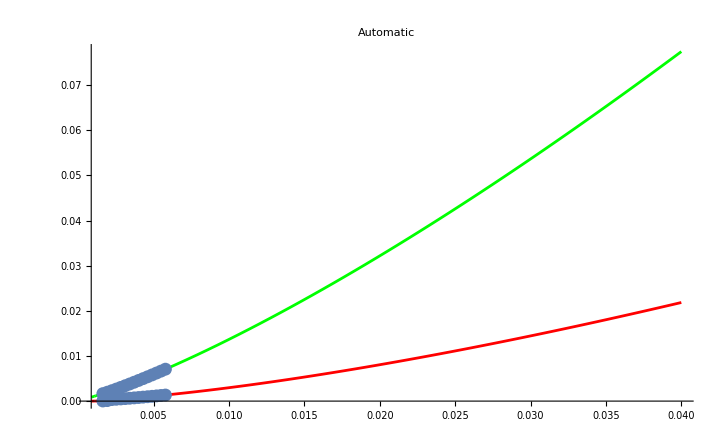

```mathematica
Plotlist={};
For[i=2,i<Length[narr]+1,i++,
(**AppendTo[Plotlist,Plot[μPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Blue]];
(**AppendTo[Plotlist,ListPlot[Transpose@{narr,μarr}]];**)
AppendTo[Plotlist,ListPlot[Transpose@{nEoSI,μEoSI}]];**)
AppendTo[Plotlist,Plot[PPP[n, Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Red]];
AppendTo[Plotlist,Plot[epsPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Green]];
(**AppendTo[Plotlist,Plot[1,{n,narr[[i-1]],narr[[i]]},PlotStyle->Black]];
AppendTo[Plotlist,Plot[csPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Purple]];**)]
AppendTo[Plotlist,ListPlot[Transpose@{nEoSIII,PEoSIII}]];
AppendTo[Plotlist,ListPlot[Transpose@{nEoSIII,ϵEoSIII}]];
(**Show[Plotlist,PlotRange->{{0,0.004},{0,0.0001}},PlotLabel->Automatic]**)
Show[Plotlist,PlotRange->All,PlotLabel->Automatic]
```

```mathematica
convmN4=101425.86
```

101426.

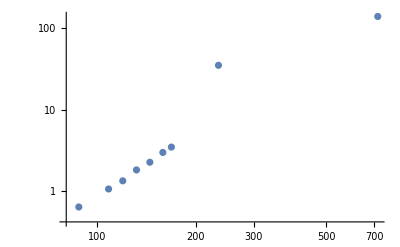

```mathematica
ListLogLogPlot[Table[{epsarr[[i]]*convmN4,Parr[[i]]*convmN4},{i,1,Length[Parr]}]]
```

```mathematica
epsarrout=epsarr[[1;;9]]*convmN4 (** 1GeV^4 in MeV/fm^3**)
Parrout=Parr[[1;;9]]*convmN4 (** 1GeV^4 in MeV/fm^3**)
Export[NotebookDirectory[]<>"output/EoS_III_points.dat",{epsarrout,Parrout}]
```

{88.0402,108.479,119.825,131.948,144.92,158.734,168.558,234.527,716.97}

{0.645837,1.07136,1.34757,1.83167,2.27248,2.99353,3.48244,34.7533,137.286}

/home/dengler_yannick/Documents/new_neutron_star_plots/TOV_final/EoS_calc/output/EoS_III_points.dat